## To Do & Notes

## Global Path Configue

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Network Project/compareFS_v0.1/NDN-EB-algo

## Read in Data

```mathematica
fileName1 = "withCScompare/best-expbf-cs-delay-trace.txt";
fileName2 = "withCScompare/best-fixed-cs-delay-trace.txt";
ipRate = 10000;
rawdata1 = Import[fileName1];
rawdata2 = Import[fileName2];
data1 = StringSplit[rawdata1,"\n"];
data2 = StringSplit[rawdata2,"\n"];
n1 = Length[data1];
n2 = Length[data2];
data21 = Table[StringSplit[row,"\t"],{row,data1}];
data22 = Table[StringSplit[row,"\t"],{row,data2}];
head1 = data21⟦1⟧;
head2 = data22⟦1⟧;
entries1 = data21⟦2;;n1⟧;
entries2 = data22⟦2;;n2⟧;
Print["Head:"];
head1
Print["Number of All Entries:"];
Length[entries1]
Length[entries2]
Print["First Several Entries:"];
entries1⟦1;;5⟧
```

Head:

{Time,Node,AppId,SeqNo,Type,DelayS,DelayUS,RetxCount,HopCount}

Number of All Entries:

46330

44070

First Several Entries:

{{0.114752,0,258,5348,LastDelay,0.114752,114752,1,4},{0.114752,0,258,5348,FullDelay,0.114752,114752,1,4},{0.12324,0,258,2180,LastDelay,0.12314,123140,1,4},{0.12324,0,258,2180,FullDelay,0.12314,123140,1,4},{0.131728,0,258,1200,LastDelay,0.131528,131528,1,4}}

## Data Preprocessing

```mathematica
(*选择需要分析的Entires*)
consumerEntries1 = Select[entries1,StringMatchQ[#⟦2⟧,"0"]&&StringMatchQ[#⟦5⟧,"FullDelay"] &];
consumerEntries2 = Select[entries2,StringMatchQ[#⟦2⟧,"0"]&&StringMatchQ[#⟦5⟧,"FullDelay"] &];
Print["Number of Sample Entries:"];
n1 = Length[consumerEntries1]
n2 = Length[consumerEntries2]
```

Number of Sample Entries:

23165

22035

```mathematica
consumerEntries1
```

{{0.114752,0,258,5348,FullDelay,0.114752,114752,1,4},{0.12324,0,258,2180,FullDelay,0.12314,123140,1,4},{0.131728,0,258,1200,FullDelay,0.131528,131528,1,4},{0.140216,0,258,568,FullDelay,0.139916,139916,1,4},23157,{149.998,0,258,194,FullDelay,0,0,1,-1},{149.999,0,258,27,FullDelay,0,0,1,-1},{149.999,0,258,3,FullDelay,0,0,1,-1},{149.999,0,258,290,FullDelay,0,0,1,-1}}
 |  |  |  |

```mathematica
Dynamic[ele]
recTimeExp = Table[Interpreter["Number"][ele⟦1⟧],{ele,consumerEntries1}];
seqNoExp = Table[Interpreter["Number"][ele⟦4⟧],{ele,consumerEntries1}];
delaySExp = Table[Interpreter["Number"][ele⟦6⟧],{ele,consumerEntries1}];
retxCountExp = Table[Interpreter["Number"][ele⟦8⟧],{ele,consumerEntries1}];
hopCountExp = Table[Interpreter["Number"][ele⟦9⟧],{ele,consumerEntries1}];

recTimeFix = Table[Interpreter["Number"][ele⟦1⟧],{ele,consumerEntries2}];
seqNoFix = Table[Interpreter["Number"][ele⟦4⟧],{ele,consumerEntries2}];
delaySFix = Table[Interpreter["Number"][ele⟦6⟧],{ele,consumerEntries2}];
retxCountFix = Table[Interpreter["Number"][ele⟦8⟧],{ele,consumerEntries2}];
hopCountFix = Table[Interpreter["Number"][ele⟦9⟧],{ele,consumerEntries2}];
```

## Save Data

```mathematica
(*Export["recTimeExp.csv",recTimeExp];
Export["seqNoExp.csv",seqNoExp];
Export["delaySExp.csv",delaySExp];
Export["retxCountExp.csv",retxCountExp];
Export["hopCountExp.csv",hopCountExp];

Export["recTimeFix.csv",recTimeFix];
Export["seqNoFix.csv",seqNoFix];
Export["delaySFix.csv",delaySFix];
Export["retxCountFix.csv",retxCountFix];
Export["hopCountFix.csv",hopCountFix];*)
```

## Load Data

```mathematica
(*recTimeExp=Flatten[Import["withCScompare_data/recTimeExp.csv"]];
seqNoExp=Flatten[Import["withCScompare_data/seqNoExp.csv"]];
delaySExp=Flatten[Import["withCScompare_data/delaySExp.csv"]];
retxCountExp=Flatten[Import["withCScompare_data/retxCountExp.csv"]];
hopCountExp=Flatten[Import["withCScompare_data/hopCountExp.csv"]];

recTimeFix=Flatten[Import["withCScompare_data/recTimeFix.csv"]];
seqNoFix=Flatten[Import["withCScompare_data/seqNoFix.csv"]];
delaySFix=Flatten[Import["withCScompare_data/delaySFix.csv"]];
retxCountFix=Flatten[Import["withCScompare_data/retxCountFix.csv"]];
hopCountFix=Flatten[Import["withCScompare_data/hopCountFix.csv"]];*)
```

## Basic Analysis

### Select the entries which has the sendTime belongs to [80, 95]

```mathematica
stableTime = 30;
duration  = 10;
sendTimeExp = Table[recTimeExp⟦i⟧-delaySExp⟦i⟧,{i,n1}];
sendTimeFix = Table[recTimeFix⟦i⟧-delaySFix⟦i⟧,{i,n2}];
indexExp = Select[Range[1,n1],sendTimeExp⟦#⟧>80&&sendTimeExp⟦#⟧≤ 95 &];
indexFix = Select[Range[1,n2],sendTimeFix⟦#⟧>80&&sendTimeFix⟦#⟧≤ 95 &];
```

```mathematica
numOfEntiresExp=Length[indexExp]
numOfEntiresFix=Length[indexFix]
```

2161

2149

```mathematica
(*1:sendtime ; 2:receivedtime; 3:delay; 4:retransmit times; 5:hopCount*)
xExp = Table[{sendTimeExp⟦i⟧,recTimeExp⟦i⟧,delaySExp⟦i⟧,retxCountExp⟦i⟧,hopCountExp⟦i⟧},{i,indexExp}];
yExp = GatherBy[xExp,#⟦5⟧&];
hopCount2delayExp = SortBy[Table[ele⟦1⟧⟦5⟧-> Mean[Table[i⟦3⟧,{i,ele}]],{ele,yExp}],First];
hopCount2retransmitTimesExp=SortBy[Table[ele⟦1⟧⟦5⟧-> N[Mean[Table[i⟦4⟧,{i,ele}]]],{ele,yExp}],First];


xFix = Table[{sendTimeFix⟦i⟧,recTimeFix⟦i⟧,delaySFix⟦i⟧,retxCountFix⟦i⟧,hopCountFix⟦i⟧},{i,indexFix}];
yFix = GatherBy[xFix,#⟦5⟧&];
hopCount2delayFix = SortBy[Table[ele⟦1⟧⟦5⟧-> Mean[Table[i⟦3⟧,{i,ele}]],{ele,yFix}],First];
hopCount2retransmitTimesFix=SortBy[Table[ele⟦1⟧⟦5⟧-> N[Mean[Table[i⟦4⟧,{i,ele}]]],{ele,yFix}],First];
```

```mathematica
hopCount2retransmitTimesExp
hopCount2retransmitTimesFix
```

{-1→1.,1→97.3066,2→91.,3→80.9318,4→78.1596,5→53.75,6→79.8519}

{-1→1.,1→92.0757,2→82.4127,3→88.4231,4→69.9559,5→77.,6→66.1463}

```mathematica
hopCount2delayExp
hopCount2delayFix
```

{-1→0,1→32.3815,2→30.8822,3→30.9988,4→25.4268,5→23.9146,6→26.9649}

{-1→0,1→31.2776,2→31.0814,3→31.3105,4→23.3981,5→28.4277,6→22.1148}

```mathematica
delayExpTotal = Mean[Table[node⟦3⟧,{node,xExp}]]
delayFixTotal = Mean[Table[node⟦3⟧,{node,xFix}]]
```

16.97

16.9155

```mathematica
retransmitTimesExpTotal = N[Mean[Table[node⟦4⟧,{node,xExp}]]]
retransmitTimesFixTotal = N[Mean[Table[node⟦4⟧,{node,xFix}]]]
```

51.2425

49.9744

```mathematica
hopWithPercentageExp=SortBy[Table[node⟦1⟧⟦5⟧-> N[Length[node]/numOfEntiresExp],{node,yExp}],First]
hopWithPercentageFix=SortBy[Table[node⟦1⟧⟦5⟧-> N[Length[node]/numOfEntiresFix],{node,yFix}],First]
```

{-1→0.449329,1→0.374364,2→0.0430356,3→0.0203609,4→0.0985655,5→0.00185099,6→0.0124942}

{-1→0.445323,1→0.461145,2→0.029316,3→0.0120987,4→0.0316426,5→0.001396,6→0.0190786}

## Export For External Analysis

```mathematica
delayExp = Table[node⟦3⟧,{node,xExp}];
delayFix = Table[node⟦3⟧,{node,xFix}];
Export["ExpdelayWithCS.csv",delayExp]
Export["FixdelayWithCS.csv",delayFix]
```

ExpdelayWithCS.csv

FixdelayWithCS.csv

2149

## Visualization

```mathematica
send2delayExp = Table[{node⟦1⟧,node⟦3⟧},{node,xExp}];
send2delayFix = Table[{node⟦1⟧,node⟦3⟧},{node,xFix}];
```

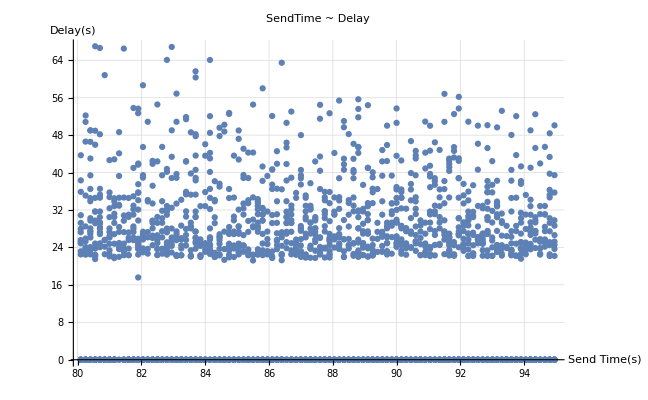

```mathematica
ListPlot[
send2delayExp,
PlotLabel ->  "SendTime ~ Delay",
AxesLabel-> {"Send Time(s)","Delay(s)"},
PlotStyle->Thin,
GridLines-> Automatic,
BaseStyle->Directive[FontSize-> 14],
ImageMargins->20
]
```

```mathematica
stableTime = 30;
duration  = 5;
sendTime = Table[recTime⟦i⟧-delayS⟦i⟧,{i,n}];
index = Select[Range[1,n],(sendTime⟦#⟧>stableTime && sendTime[#]≤ stableTime+duration)&]
sendTime2delayS = Table[{sendTime⟦i⟧,delayS⟦i⟧},{i,index}];
ListPlot[
sendTime2delayS,
PlotLabel ->  "SendTime to RecievedTime r=2",
AxesLabel-> {"Send Time(s)","Received Time(s)"}
]
```

```mathematica
sendTime2delayS
```

{}

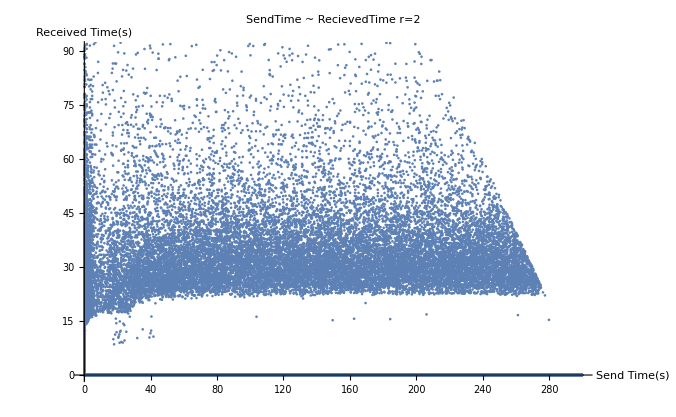

```mathematica
sendTime = Table[recTime⟦i⟧-delayS⟦i⟧,{i,n}];
sendTime2delayS = Table[{sendTime⟦i⟧,delayS⟦i⟧},{i,n}];
ListPlot[
sendTime2delayS,
PlotLabel ->  "SendTime ~ RecievedTime r=2",
AxesLabel-> {"Send Time(s)","Received Time(s)"},
(*PlotRange->{{0,5},{0,5}},*)
PlotStyle->Thin
]
```

```mathematica
Mean[
Table[
delayS⟦id⟧,
{id,Select[Range[1,n],sendTime⟦#⟧>10&]}
]
]
```

18.7084

```mathematica
N[Mean[retxCount]]
```

57.0825

## Visualization

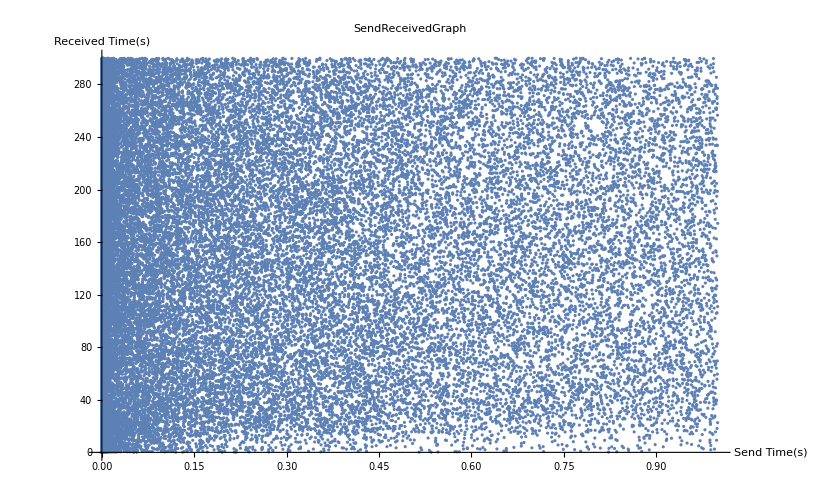

```mathematica
(*每秒传10W个interest packet，所以除以interest packet rate*)
seqNo2recTime = Table[{seqNo⟦i⟧/ipRate,recTime⟦i⟧},{i,n}];
ListPlot[seqNo2recTime,
PlotLabel ->  "SendReceivedGraph",
AxesLabel-> {"Send Time(s)","Received Time(s)"},
(*PlotRange->{{0,5},{0,5}},*)
PlotStyle->Thin
]
```

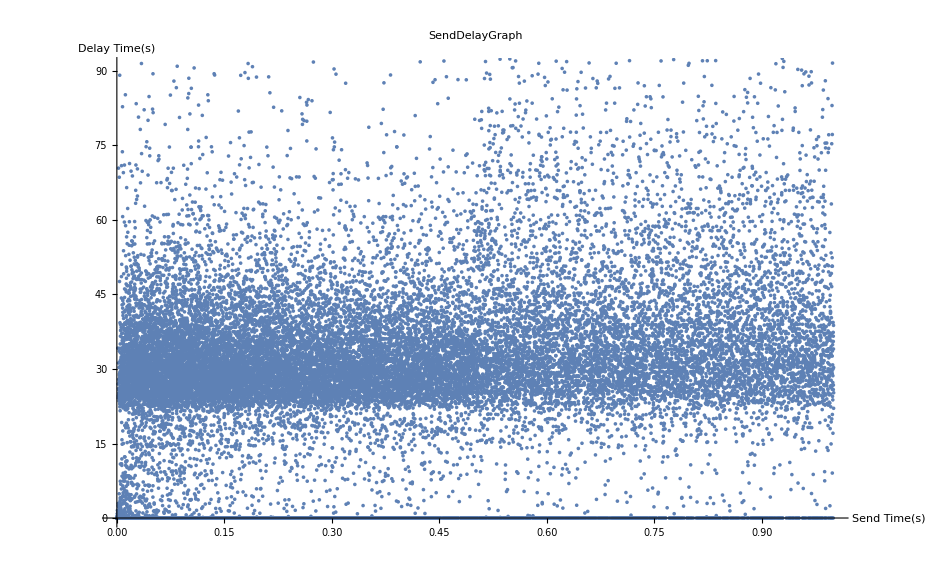

```mathematica
secNo2delayS = Table[{seqNo⟦i⟧/ipRate,delayS⟦i⟧},{i,n}];
ListPlot[secNo2delayS,
PlotLabel ->  "SendDelayGraph",
AxesLabel-> {"Send Time(s)","Delay Time(s)"},
PlotStyle->Thin
]
```

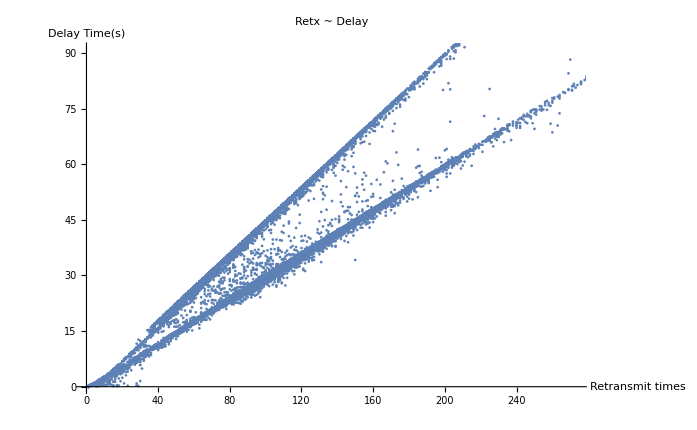

```mathematica
retxCount2delayS = Table[{retxCount⟦i⟧,delayS⟦i⟧},{i,n}];
ListPlot[retxCount2delayS,
PlotLabel ->  "Retx ~ Delay",
AxesLabel-> {Style["Retransmit times",14],Style["Delay Time(s)",14]},
PlotStyle->Thin
]
```

```mathematica
retxCount2delayS = Table[{recTime⟦i⟧,delayS⟦i⟧,retxCount⟦i⟧},{i,n}];
ListPointPlot3D[retxCount2delayS,
PlotLabel ->  "ReceivedDelayRetransmitGraph",
AxesLabel-> {"Received Times(s)","Delay Time(s)","Retransmit times"},
PlotStyle->Thin
]
```

-Graphics3D-

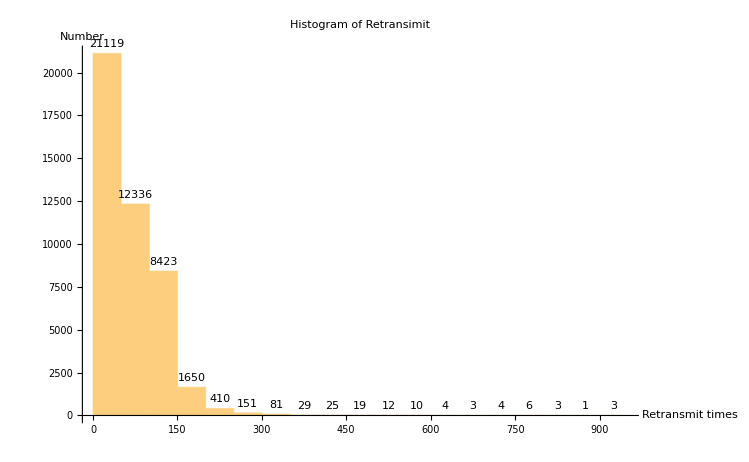

```mathematica
Histogram[retxCount,
ChartLayout->"Stacked",
PlotLabel->Style["Histogram of Retransimit","Title",14],
LabelingFunction->Above,
AxesLabel->{"Retransmit times","Number"}
]
```

```mathematica
Export["retxCount.csv",retxCount];
```

```mathematica
GridLines-> Automatic,
Joined-> True,
FrameLabel->{"Dates","PM 2.5 Value"},
PlotLabel->"PM2.5 Value in the First Quarter of 2014 and its 24 hours moving average",
BaseStyle->Directive[FontSize-> 16],
ImageMargins->20
```

```mathematica
Table[{k,PDF[BinomialDistribution[50,p],k]},{p,{0.3,0.5,0.8}},{k,0,50}]
```

{{{0,1.79847×10^-8},{1,3.85385×10^-7},{2,4.04655×10^-6},{3,0.0000277477},{4,0.00013973},{5,0.000550934},{6,0.00177086},{7,0.00477048},{8,0.0109891},{9,0.0219783},{10,0.038619},{11,0.0601854},{12,0.0838297},{13,0.105017},{14,0.118948},{15,0.122347},{16,0.1147},{17,0.0983144},{18,0.0772471},{19,0.0557573},{20,0.0370388},{21,0.0226768},{22,0.0128109},{23,0.00668396},{24,0.00322262},{25,0.00143637},{26,0.00059191},{27,0.00022549},{28,0.0000793815},{29,0.0000258088},{30,7.74263×10^-6},{31,2.14082×10^-6},{32,5.44762×10^-7},{33,1.27347×10^-7},{34,2.72886×10^-8},{35,5.34635×10^-9},{36,9.54705×10^-10},{37,1.54817×10^-10},{38,2.26987×10^-11},{39,2.99324×10^-12},{40,3.52775×10^-13},{41,3.68754×10^-14},{42,3.38652×10^-15},{43,2.70021×10^-16},{44,1.84105×10^-17},{45,1.05203×10^-18},{46,4.90076×10^-20},{47,1.78751×10^-21},{48,4.78798×10^-23},{49,8.37548×10^-25},{50,7.17898×10^-27}},{{0,8.88178×10^-16},{1,4.44089×10^-14},{2,1.08802×10^-12},{3,1.74083×10^-11},{4,2.04547×10^-10},{5,1.88184×10^-9},{6,1.41138×10^-8},{7,8.87152×10^-8},{8,4.76844×10^-7},{9,2.22527×10^-6},{10,9.12362×10^-6},{11,0.0000331768},{12,0.000107825},{13,0.000315179},{14,0.000832974},{15,0.00199914},{16,0.00437311},{17,0.00874623},{18,0.0160348},{19,0.0270059},{20,0.0418591},{21,0.0597988},{22,0.0788257},{23,0.0959617},{24,0.107957},{25,0.112275},{26,0.107957},{27,0.0959617},{28,0.0788257},{29,0.0597988},{30,0.0418591},{31,0.0270059},{32,0.0160348},{33,0.00874623},{34,0.00437311},{35,0.00199914},{36,0.000832974},{37,0.000315179},{38,0.000107825},{39,0.0000331768},{40,9.12362×10^-6},{41,2.22527×10^-6},{42,4.76844×10^-7},{43,8.87152×10^-8},{44,1.41138×10^-8},{45,1.88184×10^-9},{46,2.04547×10^-10},{47,1.74083×10^-11},{48,1.08802×10^-12},{49,4.44089×10^-14},{50,8.88178×10^-16}},{{0,1.1259×10^-35},{1,2.2518×10^-33},{2,2.20676×10^-31},{3,1.41233×10^-29},{4,6.63795×10^-28},{5,2.44276×10^-26},{6,7.32829×10^-25},{7,1.84254×10^-23},{8,3.96147×10^-22},{9,7.39474×10^-21},{10,1.21274×10^-19},{11,1.76398×10^-18},{12,2.29317×10^-17},{13,2.68125×10^-16},{14,2.83446×10^-15},{15,2.72109×10^-14},{16,2.38095×10^-13},{17,1.90476×10^-12},{18,1.39682×10^-11},{19,9.41018×10^-11},{20,5.83431×10^-10},{21,3.33389×10^-9},{22,1.75787×10^-8},{23,8.56007×10^-8},{24,3.85203×10^-7},{25,1.60244×10^-6},{26,6.16325×10^-6},{27,0.0000219138},{28,0.0000720024},{29,0.00021849},{30,0.000611772},{31,0.00157877},{32,0.00374957},{33,0.00818088},{34,0.0163618},{35,0.0299187},{36,0.0498644},{37,0.0754705},{38,0.103275},{39,0.127108},{40,0.139819},{41,0.136409},{42,0.116922},{43,0.0870116},{44,0.055371},{45,0.0295312},{46,0.0128397},{47,0.00437095},{48,0.00109274},{49,0.000178406},{50,0.0000142725}}}